```mathematica
roots=x/.NSolve[D[ChebyshevT[4,x],x]==0,x]
```

{-0.707107,0.,0.707107}

```mathematica
roots=Thread[{roots,{-1,1,-1}}]
```

{{-0.707107,-1},{0.,1},{0.707107,-1}}

```mathematica
coords={{-0.4,-1},{0.2,1},{0.4,-1}};
```

```mathematica
plot=Plot[ChebyshevT[4,x],{x,-1,1},Epilog->{Orange,AbsolutePointSize[6],Point[roots]}];
```

```mathematica
cText=Text["Centered",{0.5,0.5},align[Center]];
ce1=Text[Style[roots[[1]],Bold],coords[[1]]];
ce2=Text[Style[roots[[2]],Bold],coords[[2]]];
ce3=Text[Style[roots[[3]],Bold],coords[[3]]];
text=Graphics[{ce1,ce2,ce3}];
```

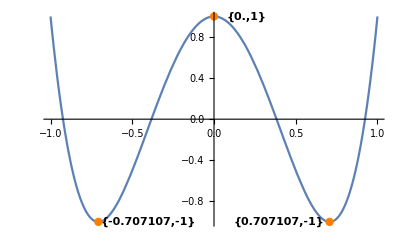

```mathematica
Show[plot,text]
```

```mathematica
ChebyshevT[4,x]
```

1-8 x^2+8 x^4

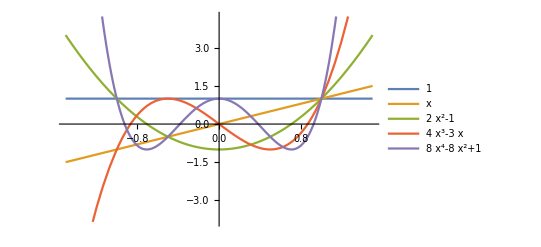

```mathematica
plot2=Plot[{1,x,2 x^2-1,4 x^3-3x,8 x^4-8 x^2+1},{x,-1.5,1.5},PlotLegends->"Expressions"]
```

```mathematica
(*Export["cheb.svg",plot2,"SVG"]*)
```

```mathematica
dataFromChebyshev={{3,8},{4,11},{5,16},{6,22},{7,30},{8,39},{9,48},{10,60},{11,72},{12,85},{13,100},{14,116},{15,132},{16,150},{17,170},{18,190},{19,211},{20,234},{21,258},{22,283},{23,309},{24,337},{25,365},{26,395},{27,426},{28,458},{29,491},{30,525},{31,561},{32,597},{33,635},{34,674},{35,714},{36,756},{37,798},{38,842},{39,887},{40,933},{41,980},{42,1028}};
```

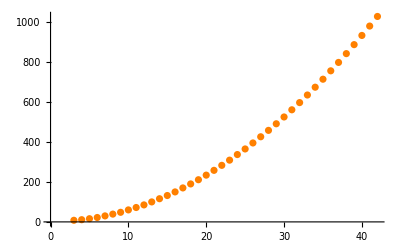

```mathematica
ListPlot[dataFromChebyshev,PlotStyle->Orange]
```

```mathematica
FindFormula[dataFromChebyshev,x]
```

1.47151+0.581984 x^2.

```mathematica
Clear[a,b,c,d,x]
```

```mathematica
NonlinearModelFit[dataFromChebyshev,a+b*x+c*x^d,{a,b,c,d},x]
```

FittedModel[2.4119-0.190521 x+0.600111 x^1.99364]

```mathematica
Clear[a,b,c,d,x]
```

```mathematica
FindFit[dataFromChebyshev,a+b*x+c*x^d,{a,b,c,d},x]
```

{a→2.4119,b→-0.190521,c→0.600111,d→1.99364}

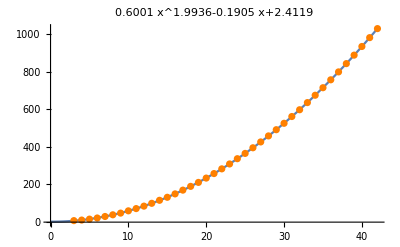

```mathematica
Show[Plot[2.4119025149683093-0.1905210352773222x+0.600111488762618 x^1.9936415326562569,{x,0,42},PlotLabel->2.4119-0.1905x+0.6001 x^1.9936],ListPlot[dataFromChebyshev,PlotStyle->Orange]]
```

```mathematica
dataFromChebyshevCorrected={{1,1},{2,3},{3,6},{4,10},{5,15},{6,21},{7,29},{8,38},{9,47},{10,58},{11,71},{12,84},{13,99},{14,114},{15,131},{16,149},{17,169},{18,189},{19,210},{20,233},{21,257},{22,282},{23,308},{24,336},{25,364},{26,394},{27,425},{28,457},{29,490},{30,524},{31,560},{32,596},{33,634},{34,673},{35,713},{36,755},{37,797},{38,841},{39,886},{40,932},{41,979},{42,1027}};
```

```mathematica
FindFormula[dataFromChebyshevCorrected,x]
```

0.331603+0.582102 x^2

```mathematica
Clear[a,b,c,d,x]
```

```mathematica
NonlinearModelFit[dataFromChebyshevCorrected,a+b*x+c*x^d,{a,b,c,d},x]
```

FittedModel[0.746895-0.0975688 x+0.591951 x^1.99647]

```mathematica
Clear[a,b,c,d,x]
```

```mathematica
FindFit[dataFromChebyshevCorrected,a+b*x+c*x^d,{a,b,c,d},x]
```

{a→0.746895,b→-0.0975688,c→0.591951,d→1.99647}

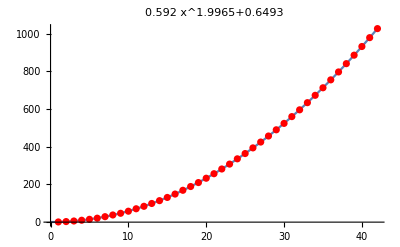

```mathematica
Show[Plot[0.7468951019078842-0.09756883681502444x+0.5919511020764084 x^1.9964736894394806,{x,0,42},PlotLabel->0.7469-0.0976+0.5920 x^1.9965],ListPlot[dataFromChebyshevCorrected,PlotStyle->Red]]
```

```mathematica
dataFromChebyshevCombined3={{1,1},{2,3},{3,8},{4,11},{5,16},{6,22},{7,30},{8,39},{9,48},{10,60},{11,72},{12,85},{13,100},{14,116},{15,132},{16,150},{17,170},{18,190},{19,211},{20,234},{21,258},{22,283},{23,309},{24,337},{25,365},{26,395},{27,426},{28,458},{29,491},{30,525},{31,561},{32,597},{33,635},{34,674},{35,714},{36,756},{37,798},{38,842},{39,887},{40,933},{41,980},{42,1028}};
```

```mathematica
FindFormula[dataFromChebyshevCombined3,x]
```

1.37093+0.582076 x^2

```mathematica
Clear[a,b,c,d,x]
```

```mathematica
FindFit[dataFromChebyshevCombined3,a+b*x+c*x^2,{a,b,c},x]
```

{a→1.37456,b→-0.000443827,c→0.582086}

```mathematica
Clear[a,b,c,x]
```

```mathematica
NonlinearModelFit[dataFromChebyshevCombined3,a+b*x+c*x^d,{a,b,c,d},x]
```

FittedModel[1.03146+0.118907 x+0.566877 x^2.00591]

```mathematica
Clear[a,b,c,d,x]
```

```mathematica
FindFit[dataFromChebyshevCombined3,a+b*x+c*x^d,{a,b,c,d},x]
```

{a→1.03146,b→0.118907,c→0.566877,d→2.00591}

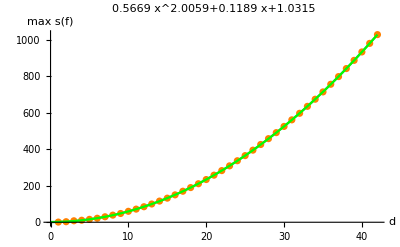

```mathematica
Show[Plot[1.0314612776275789+0.11890694947862923x+0.5668767524855678 x^2.0059089923861957,{x,0,42},PlotLabel->1.0315+0.1189x+0.5669 x^2.0059],ListPlot[dataFromChebyshevCombined3,PlotStyle->Orange],Plot[1.3709345409630735+0.5820762458190168 x^2,{x,0,42},PlotStyle->Green],AxesLabel->{"d","max s(f)"}]
```

```mathematica
dataFromChebyshevCombined15={{1,1},{2,3},{3,6},{4,10},{5,15},{6,21},{7,29},{8,38},{9,47},{10,58},{11,71},{12,84},{13,99},{14,114},{15,132},{16,150},{17,170},{18,190},{19,211},{20,234},{21,258},{22,283},{23,309},{24,337},{25,365},{26,395},{27,426},{28,458},{29,491},{30,525},{31,561},{32,597},{33,635},{34,674},{35,714},{36,756},{37,798},{38,842},{39,887},{40,933},{41,980},{42,1028}};
```

```mathematica
FindFormula[dataFromChebyshevCombined15,x]
```

0.621053+0.582721 x^2

```mathematica
Clear[a,b,c,d,x]
```

```mathematica
NonlinearModelFit[dataFromChebyshevCombined15,a+b*x+c*x^d,{a,b,c,d},x]
```

FittedModel[0.664949-0.128273 x+0.605952 x^1.99078]

```mathematica
Clear[a,b,c,d,x]
```

```mathematica
FindFit[dataFromChebyshevCombined15,a+b*x+c*x^d,{a,b,c,d},x]
```

{a→0.664949,b→-0.128273,c→0.605952,d→1.99078}

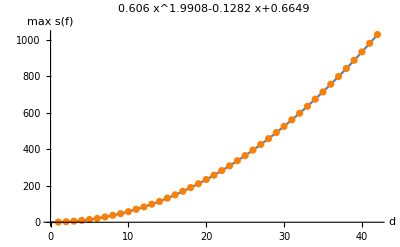

```mathematica
Show[Plot[0.6649490432294023-0.1282725992662569x+0.6059519348263525 x^1.9907845497356524,{x,0,42},PlotLabel->0.6649-0.1282x+0.6060 x^1.9908],ListPlot[dataFromChebyshevCombined15,PlotStyle->Orange],AxesLabel->{"d","max s(f)"}]
```

```mathematica
dataIneq={{2,8},{3,14},{4,22},{5,32},{6,44},{7,60},{8,78},{9,96},{10,118},{11,144},{12,170},{13,200},{14,230},{15,265},{16,300},{17,348},{18,380},{19,422},{20,468}};
```

```mathematica
Clear[a,b,d,x]
```

```mathematica
NonlinearModelFit[dataIneq,a+b*x+c*x^d,{a,b,c,d},x]
```

FittedModel[7.09413-2.23322 x+1.63646 x^1.91433]

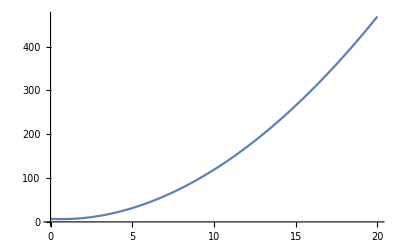

```mathematica
Plot[7.094130603469454-2.2332236770540432x+1.6364594322710404 x^1.914331015943658,{x,0,20}]
```

```mathematica
dataIneqChebyshev={{3,4},{4,12},{5,16},{6,18},{7,24},{8,28},{9,28},{10,34},{11,40},{12,44},{13,48},{14,50},{15,56},{16,58},{17,64},{18,66},{19,72},{20,74}};
```

```mathematica
Clear[a,b,d,x]
```

```mathematica
NonlinearModelFit[dataIneqChebyshev,a+b*x^d,{a,b,d},x]
```

FittedModel[-8.18512+5.06359 x^0.932788]

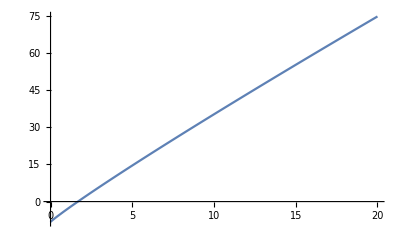

```mathematica
Plot[-8.185120610633797+5.06358815157186 x^0.9327882894264554,{x,0,20}]
```

```mathematica
dataTime={{3,1},{4,1},{5,1},{6,1},{7,1},{8,2},{9,4},{10,7},{11,12},{12,25},{13,51},{14,90},{15,139},{16,239},{17,391},{18,605},{19,954},{20,1572},{21,2564},{22,3772},{23,4905}};
```

```mathematica
Clear[a,b,d,x]
```

```mathematica
Fit[dataTime,{1,x,x^2,x^3,x^4,x^5,x^6,x^7,x^8,x^9},x]
```

2648.27-3116.55 x+1529.49 x^2-411.787 x^3+67.2568 x^4-6.93716 x^5+0.453594 x^6-0.0181953 x^7+0.000407684 x^8-3.89688×10^-6 x^9

```mathematica
Clear[a,b,d,x]
```

```mathematica
FindFormula[dataTime,x]
```

-14.8848+6.4788×10^-8 x^8

```mathematica
NonlinearModelFit[dataTime,a+b*x^d,{a,b,d},x]
```

NonlinearModelFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FittedModel[-13.4632+5.92734×10^-8 x^8.02859]

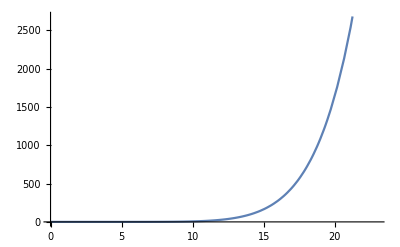

```mathematica
Plot[6.440060692653522*^-8 x^8,{x,0,23}]
```

```mathematica
dataTimeChebyshev={{3,1},{4,1},{5,1},{6,1},{7,1},{8,1},{9,1},{10,1},{11,1},{12,2},{13,2},{14,3},{15,4},{16,6},{17,9},{18,13},{19,20},{20,24},{21,35},{22,51},{23,72}};
```

```mathematica
Clear[a,b,d,x]
```

```mathematica
Fit[dataTimeChebyshev,{1,x,x^2,x^3,x^4,x^5,x^6,x^7,x^8,x^9},x]
```

137.325-150.036 x+68.092 x^2-16.7951 x^3+2.49444 x^4-0.232675 x^5+0.0137062 x^6-0.000494177 x^7+9.94267×10^-6 x^8-8.53916×10^-8 x^9

```mathematica
Clear[a,b,d,x]
```

```mathematica
FindFormula[dataTimeChebyshev,x]
```

Piecewise[{{1., 3.≤x<10.5338}, {1., 10.5338≤x<10.796}, {175.283+9.78199 x-117.278 Log[x], 10.796≤x<18.836}, {4896.62+133.375 x-2516.89 Log[x], 18.836≤x<23.}, {0, True}}]

```mathematica
NonlinearModelFit[dataTimeChebyshev,a+b*x+c*x^d,{a,b,c,d},x]
```

NonlinearModelFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FittedModel[3.05637-0.310693 x+2.57384×10^-7 x^6.20191]

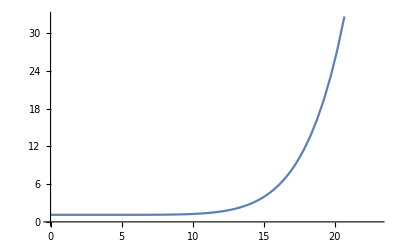

```mathematica
Plot[1.1235658633366263+4.288627389940472*^-9 x^7.5,{x,0,23}]
```

```mathematica
Limit[(2648.2683554760993-3116.5495371507304x+1529.4932458992123 x^2-411.7872998592526 x^3+67.25682746796524 x^4-6.937164127069844 x^5+0.4535940049178452 x^6-0.018195254070421187 x^7)/(137.3246528064107-150.03635701370368x+68.09197591893137 x^2-16.79509000666751 x^3+2.4944367839688684 x^4-0.23267525180331242 x^5+0.013706220916153642 x^6-0.0004941770817379043 x^7),x->∞]
```

36.8193

```mathematica
dataTimeDifference={{3,1},{4,1},{5,1},{6,1},{7,1},{8,2},{9,4},{10,7},{11,12},{12,13},{13,25},{14,30},{15,35},{16,40},{17,43},{18,48},{19,49},{20,65},{21,73},{22,74},{23,68}};
```

```mathematica
Clear[a,b,d,x]
```

```mathematica
FindFormula[dataTimeDifference,x]
```

Piecewise[{{1., 3.≤x<6.05327}, {-18.7429+2.65714 x, 6.05327≤x<12.7437}, {-40.+5. x, 12.7437≤x<14.9405}, {-27.8+4.2 x, 14.9405≤x<18.3873}, {-6529.31-145.946 x+3170.82 Log[0.0901187+x], 18.3873≤x<23.}, {0, True}}]

```mathematica
Fit[dataTimeDifference,{1,x,x^2,x^3,x^4,x^5,x^6,x^7,x^8,x^9},x]
```

-476.614+529.958 x-242.833 x^2+60.5315 x^3-9.08487 x^4+0.854743 x^5-0.0505945 x^6+0.0018249 x^7-0.0000365677 x^8+3.1159×10^-7 x^9

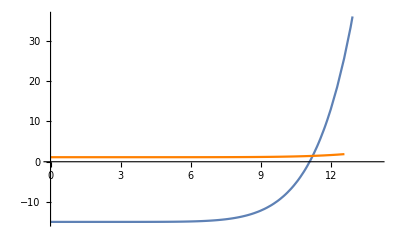

```mathematica
Show[Plot[-14.884751370707502+6.478803856639619*^-8 x^8,{x,0,14}],Plot[1.1235658633366263+4.288627389940472*^-9 x^7.5,{x,0,14},PlotStyle->Orange]]
```

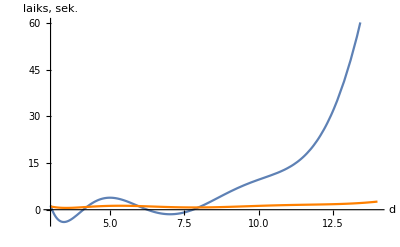

```mathematica
Show[Plot[2648.2683554760993-3116.5495371507304x+1529.4932458992123 x^2-411.7872998592526 x^3+67.25682746796524 x^4-6.937164127069844 x^5+0.4535940049178452 x^6-0.018195254070421187 x^7+0.000407684172239597 x^8-3.896880767386559*^-6 x^9,{x,3,14}],Plot[137.3246528064107-150.03635701370368x+68.09197591893137 x^2-16.79509000666751 x^3+2.4944367839688684 x^4-0.23267525180331242 x^5+0.013706220916153642 x^6-0.0004941770817379043 x^7+9.942668726027924*^-6 x^8-8.539155510794079*^-8 x^9,{x,3,14},PlotStyle->Orange],AxesLabel->{"d","laiks, sek."},PlotRange->All]
```

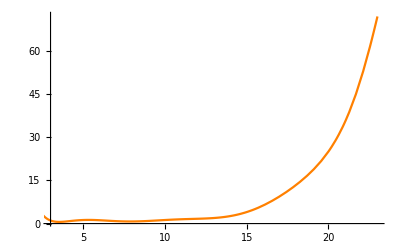

```mathematica
Plot[Piecewise[{{0,x<2},{137.3246528064107-150.03635701370368x+68.09197591893137 x^2-16.79509000666751 x^3+2.4944367839688684 x^4-0.23267525180331242 x^5+0.013706220916153642 x^6-0.0004941770817379043 x^7+9.942668726027924*^-6 x^8-8.539155510794079*^-8 x^9,x≥2}}],{x,2,23},PlotRange->{{3,23},All},PlotStyle->Orange]
```

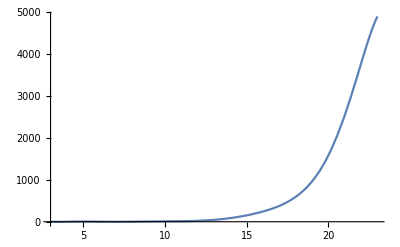

```mathematica
Plot[Piecewise[{{0,x<3},{2648.2683554760993-3116.5495371507304x+1529.4932458992123 x^2-411.7872998592526 x^3+67.25682746796524 x^4-6.937164127069844 x^5+0.4535940049178452 x^6-0.018195254070421187 x^7+0.000407684172239597 x^8-3.896880767386559*^-6 x^9,x≥3}}],{x,3,23},PlotRange->{{3,23},All}]
```

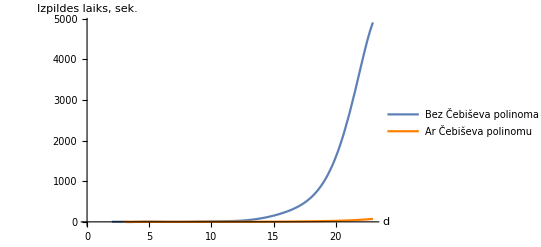

```mathematica
plot3=Show[Plot[Piecewise[{{Undefined,x<2},{x,x<3},{2648.2683554760993-3116.5495371507304x+1529.4932458992123 x^2-411.7872998592526 x^3+67.25682746796524 x^4-6.937164127069844 x^5+0.4535940049178452 x^6-0.018195254070421187 x^7+0.000407684172239597 x^8-3.896880767386559*^-6 x^9,x≥3}}],{x,0,23},PlotLegends->{"Bez Čebiševa polinoma"},PlotRange->{{0,23},All}],Plot[Piecewise[{{Undefined,x<3},{137.3246528064107-150.03635701370368x+68.09197591893137 x^2-16.79509000666751 x^3+2.4944367839688684 x^4-0.23267525180331242 x^5+0.013706220916153642 x^6-0.0004941770817379043 x^7+9.942668726027924*^-6 x^8-8.539155510794079*^-8 x^9,x≥3}}],{x,0,23},PlotLegends->{"Ar Čebiševa polinomu"},PlotStyle->Orange,PlotRange->{{0,23},All}],AxesLabel->{"d","Izpildes laiks, sek."}]
```

```mathematica
(*Export["cheb2.svg",plot3,"SVG"]*)
```

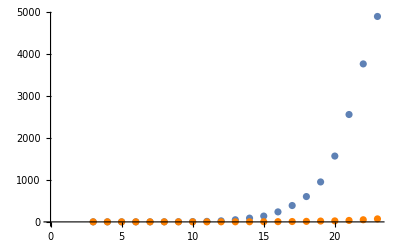

```mathematica
Show[ListPlot[dataTime],ListPlot[dataTimeChebyshev,PlotStyle->Orange]]
```